```mathematica
Hs={{ϵ,Δ},{Δ,-ϵ}}/2
PauliMatrix[3]
FullSimplify[MatrixExp[-I t Hs].PauliMatrix[3].MatrixExp[I t Hs]]//MatrixForm
```

{{ϵ/2,Δ/2},{Δ/2,-ϵ/2}}

{{1,0},{0,-1}}

((ϵ^2+Δ^2 Cos[t √(Δ^2+ϵ^2)])/(Δ^2+ϵ^2) | (Δ (ϵ-ϵ Cos[t √(Δ^2+ϵ^2)]+ⅈ √(Δ^2+ϵ^2) Sin[t √(Δ^2+ϵ^2)]))/(Δ^2+ϵ^2)
(Δ (ϵ-ϵ Cos[t √(Δ^2+ϵ^2)]-ⅈ √(Δ^2+ϵ^2) Sin[t √(Δ^2+ϵ^2)]))/(Δ^2+ϵ^2) | -(ϵ^2+Δ^2 Cos[t √(Δ^2+ϵ^2)])/(Δ^2+ϵ^2))

```mathematica
FullSimplify[(Δ (ϵ-ϵ Cos[t √(Δ^2+ϵ^2)]-ⅈ √(Δ^2+ϵ^2) Sin[t √(Δ^2+ϵ^2)]))/(Δ^2+ϵ^2)]
```

(Δ (ϵ-ϵ Cos[t √(Δ^2+ϵ^2)]-ⅈ √(Δ^2+ϵ^2) Sin[t √(Δ^2+ϵ^2)]))/(Δ^2+ϵ^2)

```mathematica
Hs=(Δ/2) PauliMatrix[1]
FullSimplify[MatrixExp[-I Hs].PauliMatrix[3].MatrixExp[I Hs]]//MatrixForm
```

{{0,Δ/2},{Δ/2,0}}

(Cos[Δ] | ⅈ Sin[Δ]
-ⅈ Sin[Δ] | -Cos[Δ])

```mathematica
MatrixExp[-I Hs].PauliMatrix[3]
```

{{Cos[Δ/2],ⅈ Sin[Δ/2]},{-ⅈ Sin[Δ/2],-Cos[Δ/2]}}

```mathematica
+++++++
```

t is ωc τ and beta is βωc and BcorrOhmic is the correlation in units ηωc^2

```mathematica
BcorrOhmic[t_,β_]:=NIntegrate[x Exp[-x](Coth[β x/2]Cos[t x]-I Sin[t x]),{x,0,Infinity}]
BcorrOhmic[1,1]
```

0.926-0.5 ⅈ

ΓOhmic is the correlation Fourier transform in units ηωc, a=Ω0/ωc

```mathematica
ΓOhmic[a_,β_]:=NIntegrate[BcorrOhmic[t,β]Exp[I a t],{t,0,Infinity}]
```

```mathematica
Plot[Re[ΓOhmic[1,β]],{β,0.5,2}]
```

NIntegrate::inumr: The integrand ⅇ^-x x (Cos[t x] Coth[0.250015 x]-ⅈ Sin[t x]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

```mathematica
Re[ΓOhmic[1,1]]
Im[ΓOhmic[1,1]]
```

NIntegrate::inumr: The integrand ⅇ^-x x (Cos[t x] Coth[x/2]-ⅈ Sin[t x]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

1.82833

NIntegrate::inumr: The integrand ⅇ^-x x (Cos[t x] Coth[x/2]-ⅈ Sin[t x]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

0.886808

```mathematica
ρ11[t_,ρ0_,γ_,ρinf_]:=ρ0 Exp[-γ t]+ρinf(1-Exp[-γ t])
```

```mathematica
a=1;
β=1;
ρ11[t,1,2Im[ΓOhmic[a,β]],1/(Exp[β a]+1)]
```

NIntegrate::inumr: The integrand ⅇ^-x x (Cos[t x] Coth[x/2]-ⅈ Sin[t x]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

ⅇ^(-1.77362 t)+(1-ⅇ^(-1.77362 t))/(1+ⅇ)

```mathematica
Plot[ρ11[t,1,2Im[ΓOhmic[a,β]],1/(Exp[β a]+1)],{t,0,1}]
```

NIntegrate::inumr: The integrand ⅇ^-x x (Cos[t x] Coth[x/2]-ⅈ Sin[t x]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted

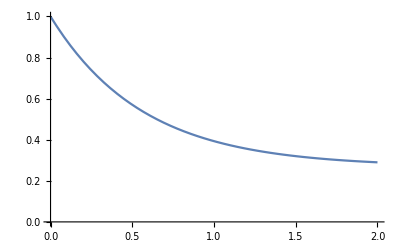

```mathematica
Plot[ⅇ^(-1.773615820308604 t)+(1-ⅇ^(-1.773615820308604 t))/(1+ⅇ),{t,0,2},PlotRange->{0,1}]
```

Equations (36,37) of the article, η=αωc

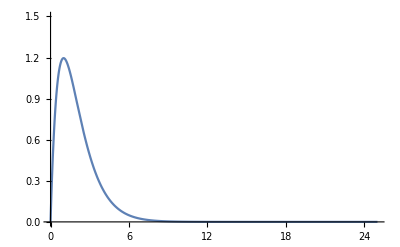

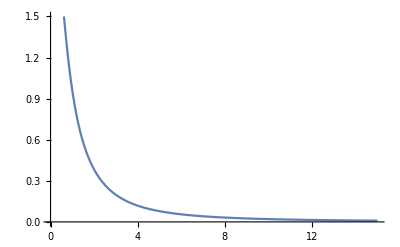

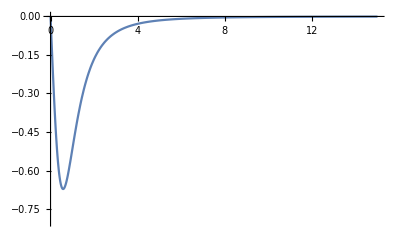

```mathematica
JOhmic[ω_,η_,s_]:=η (ω)^s Exp[-ω]
COhmic[t_,α_,β_,s_]:=1/Pi α β^(-(s+1))Gamma[s+1](Zeta[s+1,(1+β-I t)/β]+Zeta[s+1,(1+I t)/β])
Plot[JOhmic[ω,3.25,1],{ω,0,25},PlotRange->{0,1.5}]
Plot[Re[COhmic[t,3.25,1,1]],{t,0,15},PlotRange->{0,1.5}]
Plot[Im[COhmic[t,3.25,1,1]],{t,0,15},PlotRange->{-.8,0}]
```

```mathematica
1/2
```

1/2

```mathematica
x^#
```

x^#1

```mathematica
Gamma[40]
39!
```

20397882081197443358640281739902897356800000000

20397882081197443358640281739902897356800000000

```mathematica
Im[COhmic[14,3.25,1,1]]
```

-0.000746378

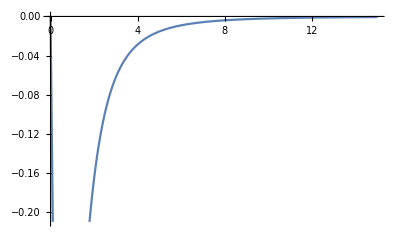

```mathematica
Plot[Im[COhmic[t,3.25,1,1]],{t,0,15}]
```

## Ohmic bath spectral density

The bath correlation function in units ηωc^2, where u=ω/ωc and β=βωc and τ=ωcτ

```mathematica
Bnumeric[τ_,β_]:=NIntegrate[u Exp[-u](Coth[β u/2]Cos[u τ]-I Sin[u τ]),{u,0,Infinity}]
Banalytic[τ_,β_]:=1/β^2(Zeta[2,1/β+I τ/β ]+Zeta[2,1/β+1-I τ/β ])
```

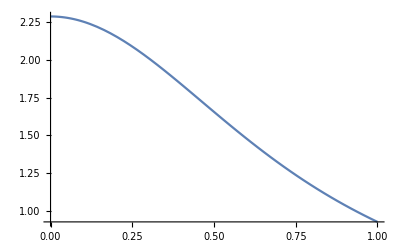

-Graphics-

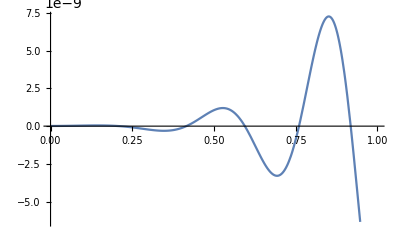

```mathematica
Plot[Re[Bnumeric[t,1]],{t,0,1}]
Plot[Re[Banalytic[t,1]],{t,0,1}]
Plot[Re[Bnumeric[t,1]-Banalytic[t,1]],{t,0,1}]
```

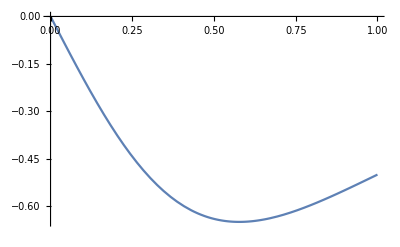

-Graphics-

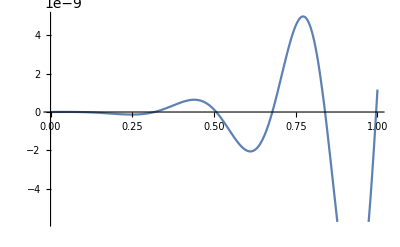

```mathematica
Plot[Im[Bnumeric[t,1]],{t,0,1}]
Plot[Im[Banalytic[t,1]],{t,0,1}]
Plot[Im[Bnumeric[t,1]]-Im[Banalytic[t,1]],{t,0,1}]
```

The one side Fourier transform of  bath correlation function in units ηωc, where a = Ω0/ωc and β = βωc and τ = ωcτ

```mathematica
Γnumeric[α_,β_]:=NIntegrate[Bnumeric[τ,β]Exp[I α τ],{τ,0,Infinity}]
Γanalytic[α_,β_]:=NIntegrate[Banalytic[τ,β]Exp[I α τ],{τ,0,Infinity}]
```

NIntegrate::inumr: The integrand ⅇ^-u u (Cos[u τ] Coth[u/2]-ⅈ Sin[u τ]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::deorela: The relative error 2.83388 is larger than expected for the integrand 1. Cos[0.0000204286 τ] NIntegrate[u Exp[-u] (Coth[1 Times[«2»]] Cos[u Plus[«2»]]-ⅈ Sin[Times[«2»]]),{u,0,∞}] over {0,∞} with DoubleExponentialOscillatory method and automatic tuning parameters, TuningParameters -> {10,5}. The integration will proceed with TuningParameters -> {1,5}.

$Aborted

NIntegrate::deorela: The relative error 2.83388 is larger than expected for the integrand 1. Cos[0.0000204286 τ] (Zeta[2,2-ⅈ (0.+τ)]+Zeta[2,1+ⅈ (0.+τ)]) over {0,∞} with DoubleExponentialOscillatory method and automatic tuning parameters, TuningParameters -> {10,5}. The integration will proceed with TuningParameters -> {1,5}.

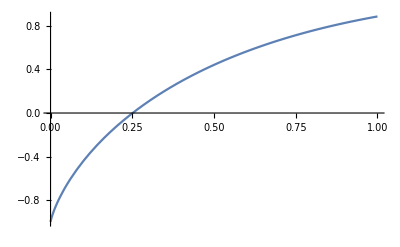

```mathematica
Plot[Im[Γnumeric[α,1]],{α,0,1}]
Plot[Im[Γanalytic[α,1]],{α,0,1}]
```

```mathematica
γminusnum[α_,β_]:= Γanalytic[α,β]+Conjugate[Γanalytic[α,β]]
γminusana[α_,β_]:=(2π α Exp[-α])/(1-Exp[-β α])
```

NIntegrate::deorela: The relative error 3.92645 is larger than expected for the integrand 0.25 Cos[0.0000204286 τ] (Zeta[2,3/2-1/2 ⅈ (0.+τ)]+Zeta[2,1/2+1/2 ⅈ (0.+τ)]) over {0,∞} with DoubleExponentialOscillatory method and automatic tuning parameters, TuningParameters -> {10,5}. The integration will proceed with TuningParameters -> {1,5}.

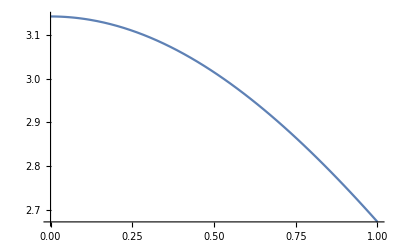

-Graphics-

```mathematica
Plot[γminusnum[α,2],{α,0,1}]
Plot[γminusana[α,2],{α,0,1}]
```

NIntegrate::deorela: The relative error 2.83388 is larger than expected for the integrand 1. Cos[0.0000204286 τ] (Zeta[2,2-ⅈ (0.+τ)]+Zeta[2,1+ⅈ (0.+τ)]) over {0,∞} with DoubleExponentialOscillatory method and automatic tuning parameters, TuningParameters -> {10,5}. The integration will proceed with TuningParameters -> {1,5}.

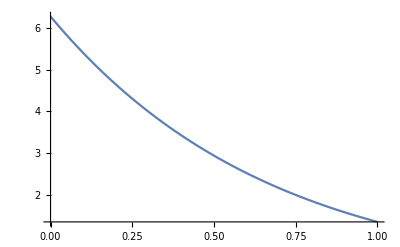

-Graphics-

```mathematica
γplusnum[α_,β_]:= Γanalytic[-α,β]+Conjugate[Γanalytic[-α,β]]
γplusana[α_,β_]:=(2π α Exp[-α]Exp[-β α])/(1-Exp[-β α])
Plot[γplusnum[α,1],{α,0,1}]
Plot[γplusana[α,1],{α,0,1}]
```

```mathematica
γnum[α_,β_]:=γplusnum[α,β]+γminusnum[α,β]
γOhmic[α_,β_]:=2π α Exp[-α]Coth[β α/2]
```

NIntegrate::deorela: The relative error 2.83388 is larger than expected for the integrand 1. Cos[0.0000204286 τ] (Zeta[2,2-ⅈ (0.+τ)]+Zeta[2,1+ⅈ (0.+τ)]) over {0,∞} with DoubleExponentialOscillatory method and automatic tuning parameters, TuningParameters -> {10,5}. The integration will proceed with TuningParameters -> {1,5}.

General::stop: Further output of NIntegrate::deorela will be suppressed during this calculation.

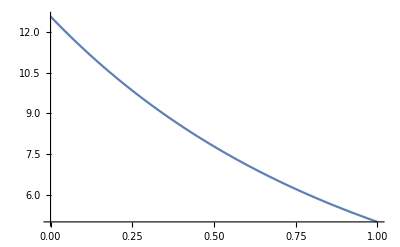

-Graphics-

```mathematica
Plot[γnum[α,1],{α,0,1}]
Plot[γOhmic[α,1],{α,0,1}]
```

Let us define the Lamb shift who wil not have an analytical expression so basically they just can be computed numerically

```mathematica
Sminusnum[α_,β_]:= 1/I(Γanalytic[α,β]-Conjugate[Γanalytic[α,β]])
Splusnum[α_,β_]:= 1/I(Γanalytic[-α,β]-Conjugate[Γanalytic[-α,β]])
Stot[α_,β_]:=Sminusnum[α,β]-Splusnum[α,β]
```

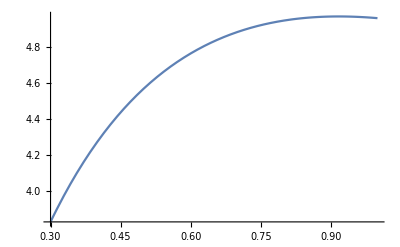

```mathematica
Plot[Stot[α,1],{α,0.3,1}]
```

Finally let’s plot the population and coherences for the Markovian case for Ohmic bath spectral density. We are assuming ηωc=1

```mathematica
1/2
```

1/2

```mathematica
ρ11Ohmic[t_,ρ0_,α_,β_]:=ρ0*Exp[-γOhmic[α,β]t]+1/(Exp[α β]+1)(1-Exp[-γOhmic[α,β]t])
ρ01Ohmic[t_,ρ0_,α_,β_]:=ρ0*Exp[1/2(I Stot[α,β]-γOhmic[α,β])t ]
```

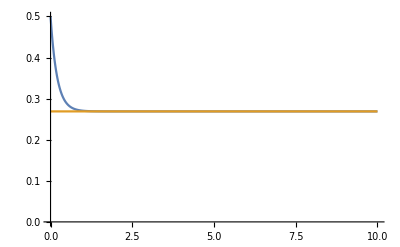

```mathematica
Plot[{ρ11Ohmic[t,1/2,1,1],1/(Exp[1]+1)},{t,0,10},PlotRange->{0,0.5}]
```

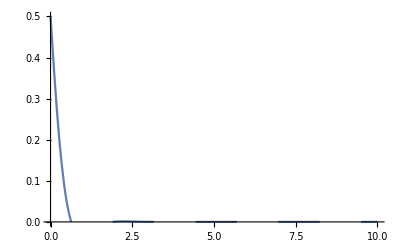

```mathematica
Plot[{Re[ρ01Ohmic[t,1/2,1,1]]},{t,0,10},PlotRange->{0,0.5}]
```

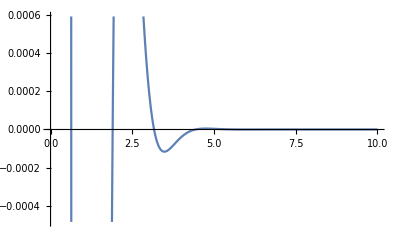

```mathematica
Plot[Re[Exp[1/2(I Stot[1,1]-γOhmic[1,1])t ]],{t,0,10}]
```

-Graphics-

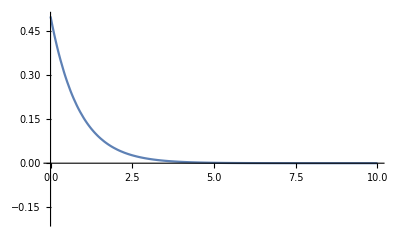

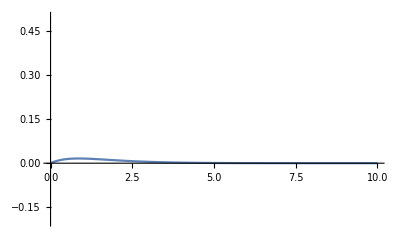

```mathematica
Plot[Re[Exp[(-2.500940143931191+2.480093542417912 ⅈ)t ]],{t,0,10}]
Plot[0.5Re[Exp[(-1.1557273497909217+0.10083409112826758 ⅈ)t ]],{t,0,10},PlotRange->{-0.2,0.5}]
Plot[0.5Im[Exp[(-1.1557273497909217+0.10083409112826758 ⅈ)t ]],{t,0,10},PlotRange->{-0.2,0.5}]
```

```mathematica
1/2(I Stot[1,1000]-γOhmic[1,1000])
```

-1.15573+0.100834 ⅈ

No salio, no queda lo que yo espero que quede

```mathematica
N[γOhmic[1,1000]]
```

2.31145

```mathematica
N[(2 π)/ⅇ]
```

2.31145

```mathematica
2.3114546995818435/2
```

1.15573

```mathematica
Sminusnum[1,1000]
Splusnum[1,1000]
```

-0.605644+0. ⅈ

-0.807312+0. ⅈ

From the previous paper

```mathematica
SXia[a_]:=-2a Exp[-a]ExpIntegralEi[a]-2
N[SXia[1]]
```

-3.39435

```mathematica
1/2
```

1/2

```mathematica
Clear[a]
```

```mathematica
Integrate[Cos[a(t-t1)],{t1,0,t}]
```

Sin[a t]/a

```mathematica
Integrate[Sin[a(t-t1)],{t1,0,t}]
```

(1-Cos[a t])/a

## TCL

#### Ohmic Bath

Let us define the decay rate for TCL 2 (aparentemente es Redfield, checar) for the Ohmic case

```mathematica
γOhmic[α_,β_]:=2π α Exp[-α]Coth[β α/2]
γ2TCLOhmic[t_,α_,β_]:=2 NIntegrate[u Exp[-u]Coth[β u/2] Sin[(u-α)t]/(u-α),{u,0,Infinity}]
```

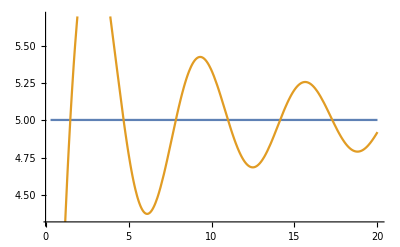

```mathematica
Plot[{γOhmic[1,1],γ2TCLOhmic[t,1,1]},{t,0.3,20}]
```

Now the decay rate for excitation plus (which will be used for the asymptotic state γplus/γ) for the Ohmic case

```mathematica
γplusana[α_,β_]:=(2π α Exp[-α]Exp[-β α])/(1-Exp[-β α])
γ2TCLplusOhmic[t_,α_,β_]:=2 NIntegrate[u Exp[-u] Exp[-β u]/(1-Exp[-β u])Sin[(u-α)t]/(u-α),{u,0,Infinity}]
```

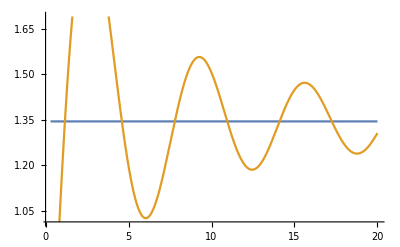

```mathematica
Plot[{γplusana[1,1],γ2TCLplusOhmic[t,1,1]},{t,0.3,20}]
```

Let' s compare the Markovian approximation with TCL, first the excited state population

```mathematica
ρ11OhmicMarkov[t_,ρ0_,α_,β_]:=ρ0*Exp[-γOhmic[α,β]t]+1/(Exp[α β]+1)(1-Exp[-γOhmic[α,β]t])
```

```mathematica
int1[tp_?NumericQ,α_,β_]:=int1[tp,α,β]=NIntegrate[γ2TCLOhmic[tpp,α,β],{tpp,0,tp}]

int2[t_?NumericQ,α_,β_]:=int2[t,α,β]=NIntegrate[γ2TCLplusOhmic[tp,α,β]Exp[int1[tp,α,β]],{tp,0,t}]

ρ11OhmicTCL2[t_,ρ0_,α_,β_]:=Exp[-int1[t,α,β]](ρ0+int2[t,α,β])
```

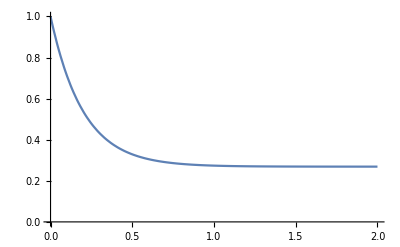

```mathematica
ρ0p=1;
αp=1;
βp=1;
Plot[ρ11OhmicMarkov[t,ρ0p,αp,βp],{t,0,2},PlotRange->{0,1}]
```

```mathematica
ρ0p=1;
αp=1;
βp=1;
Plot[ρ11OhmicTCL2[t,ρ0p,αp,βp],{t,0,2},PlotRange->{0,1}]
```

NIntegrate::inumr: The integrand (ⅇ^-u u Coth[u/2] Sin[tpp (-1+u)])/(-1+u) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.